```mathematica
cblack={{0.1,0.5},{0.35,0.75}};
cred={{0.28,1.35}};
cblue={{0,1.01}};
alldata=Join[Subscript[cluster, Black],Subscript[cluster, Red],Subscript[cluster, Blue]];
```

```mathematica
Subscript[mu, Black]={0.225,0.625};
Subscript[mu, Red]={0.28,1.35};
Subscript[mu, Blue]={0,1.01};
```

```mathematica
l1norm[p1_]:=Norm[p1,1]
l2norm[p1_]:=Norm[p1,2]
linfnorm[p1_]:=Norm[p1,Infinity]
```

## 1.

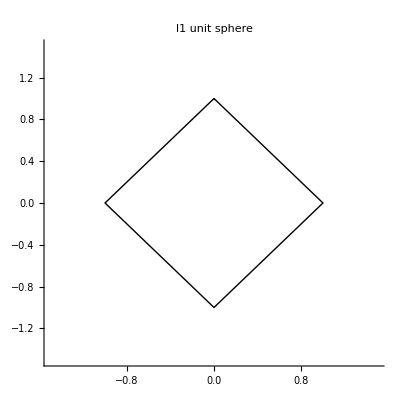

```mathematica
Graphics[Line[{{0,1},{1,0},{0,-1},{-1,0},{0,1}}],Axes->True,PlotLabel->"l1 unit sphere",PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

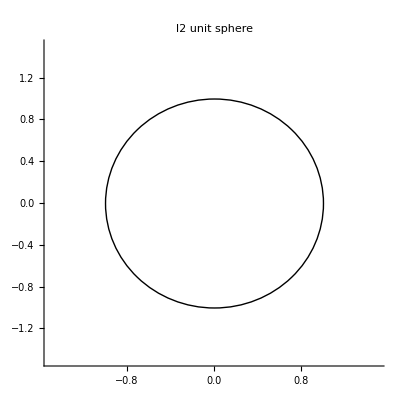

```mathematica
Graphics[Circle[{0,0},1],Axes->True,PlotLabel->"l2 unit sphere",PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

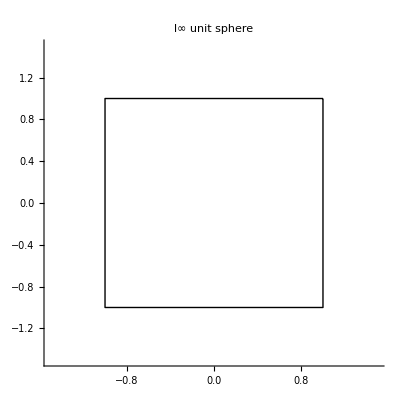

```mathematica
Graphics[Line[{{1,1},{1,-1},{-1,-1},{-1,1},{1,1}}],Axes->True,PlotLabel->"l∞ unit sphere",PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

## 2.

```mathematica
(*l1*)
l1norm[cblack[[1]]-cred[[1]]]
l1norm[cblack[[2]]-cred[[1]]]
l1norm[cblack[[1]]-cblue[[1]]]
l1norm[cblack[[2]]-cblue[[1]]]
l1norm[cblue[[1]]-cred[[1]]]
```

1.03

0.67

0.61

0.61

0.62

```mathematica
(*l2*)
l2norm[cblack[[1]]-cred[[1]]]
l2norm[cblack[[2]]-cred[[1]]]
l2norm[cblack[[1]]-cblue[[1]]]
l2norm[cblack[[2]]-cblue[[1]]]
l2norm[cblue[[1]]-cred[[1]]]
```

0.86885

0.60407

0.519711

0.436005

0.440454

```mathematica
(*linf*)
linfnorm[cblack[[1]]-cred[[1]]]
linfnorm[cblack[[2]]-cred[[1]]]
linfnorm[cblack[[1]]-cblue[[1]]]
linfnorm[cblack[[2]]-cblue[[1]]]
linfnorm[cblue[[1]]-cred[[1]]]
```

0.85

0.6

0.51

0.35

0.34

```mathematica
(*l1, centroid*)
l1norm[Subscript[mu, Black]-Subscript[mu, Blue]]
l1norm[Subscript[mu, Black]-Subscript[mu, Red]]
l1norm[Subscript[mu, Blue]-Subscript[mu, Red]]
```

0.61

0.78

0.62

```mathematica
(*l2, centroid*)
l2norm[Subscript[mu, Black]-Subscript[mu, Blue]]
l2norm[Subscript[mu, Black]-Subscript[mu, Red]]
l2norm[Subscript[mu, Blue]-Subscript[mu, Red]]
```

0.445926

0.727083

0.440454

```mathematica
(*linf, centroid*)
linfnorm[Subscript[mu, Black]-Subscript[mu, Blue]]
linfnorm[Subscript[mu, Black]-Subscript[mu, Red]]
linfnorm[Subscript[mu, Blue]-Subscript[mu, Red]]
```

0.385

0.725

0.34

```mathematica
(*l1, avg*)
Mean[{l1norm[cblack[[1]]-cred[[1]]],l1norm[cblack[[2]]-cred[[1]]]}]
Mean[{l1norm[cblack[[1]]-cblue[[1]]],l1norm[cblack[[2]]-cblue[[1]]]}]
Mean[{l1norm[cblue[[1]]-cred[[1]]]}]
```

0.85

0.61

0.62

```mathematica
(*l2, avg*)
Mean[{l2norm[cblack[[1]]-cred[[1]]],l2norm[cblack[[2]]-cred[[1]]]}]
Mean[{l2norm[cblack[[1]]-cblue[[1]]],l2norm[cblack[[2]]-cblue[[1]]]}]
Mean[{l2norm[cblue[[1]]-cred[[1]]]}]
```

0.73646

0.477858

0.440454

```mathematica
(*linf, avg*)
Mean[{linfnorm[cblack[[1]]-cred[[1]]],linfnorm[cblack[[2]]-cred[[1]]]}]
Mean[{linfnorm[cblack[[1]]-cblue[[1]]],linfnorm[cblack[[2]]-cblue[[1]]]}]
Mean[{linfnorm[cblue[[1]]-cred[[1]]]}]
```

0.725

0.43

0.34

## 3.

```mathematica
(*l2*)
l2norm[cblack[[1]]-cred[[1]]]
l2norm[cblack[[2]]-cred[[1]]]
l2norm[cblack[[1]]-cblue[[1]]]
l2norm[cblack[[2]]-cblue[[1]]]
l2norm[cblue[[1]]-cred[[1]]]
```

0.86885

0.60407

0.519711

0.436005

0.440454

```mathematica
(*l2, centroid*)
l2norm[Subscript[mu, Black]-Subscript[mu, Blue]]
l2norm[Subscript[mu, Black]-Subscript[mu, Red]]
l2norm[Subscript[mu, Blue]-Subscript[mu, Red]]

l2norm[(Subscript[mu, Blue]+Subscript[mu, Red])/2-Subscript[mu, Black]]
```

0.445926

0.727083

0.440454

0.561471

```mathematica
(*l2, avg*)
Mean[{l2norm[cblack[[1]]-cred[[1]]],l2norm[cblack[[2]]-cred[[1]]]}]
Mean[{l2norm[cblack[[1]]-cblue[[1]]],l2norm[cblack[[2]]-cblue[[1]]]}]
Mean[{l2norm[cblue[[1]]-cred[[1]]]}]

Mean[{l2norm[cblack[[1]]-cred[[1]]],l2norm[cblack[[2]]-cred[[1]]],l2norm[cblack[[1]]-cblue[[1]]],l2norm[cblack[[2]]-cblue[[1]]]}]
```

0.73646

0.477858

0.440454

0.607159

```mathematica
black=0
blue=0.436005
red=0.436005+0.440454
```

0

0.436005

0.876459

```mathematica
(*l1norm[data_]:=Total[Table[Norm[data[[i]]],{i,1,Length[data]}]]
l2norm[data_]:=√Total[Table[(Norm[data[[i]]])^2,{i,1,Length[data]}]]
linfnorm[data_]:=Max[Table[(Norm[data[[i]]])^2,{i,1,Length[data]}]]*)
```

```mathematica
?Dendrogram
```

RowBox[{"Dendrogram", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", "…"}], "}"}], "]"}] constructs a dendrogram from the hierarchical clustering of the elements SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Dendrogram", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]]}], ",", "…"}], "}"}], "]"}] represents SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] with SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] in the constructed dendrogram.
RowBox[{"Dendrogram", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", "…"}], "}"}], "→", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", "…"}], "}"}]}], "]"}] represents SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] with SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] in the constructed dendrogram.
RowBox[{RowBox[{"Dendrogram", "[", RowBox[{"<|", RowBox[{SubscriptBox[StyleBox["label", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["label", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]]}], ",", "…"}], "|>"}], "]"}] represents SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] using labels SubscriptBox[StyleBox["label", "TI"], StyleBox["i", "TI"]] in the constructed dendrogram.
RowBox[{"Dendrogram", "[", RowBox[{StyleBox["data", "TI"], ",", StyleBox["orientation", "TI"]}], "]"}] constructs an oriented dendrogram according to StyleBox["orientation", "TI"].
RowBox[{"Dendrogram", "[", StyleBox["tree", "TI"], "]"}] constructs the dendrogram corresponding to weighted tree StyleBox["tree", "TI"].

```mathematica
Dendrogram[{{{1,2},{2,4}},{{2,6}}}]
```

Dendrogram::nodis: Dendrogram was unable to compute positive and real pairwise distances for {{{1,2},{2,4}},{{2,6}}}.

Dendrogram[{{{1,2},{2,4}},{{2,6}}}]